```mathematica
dPhi=941;Tm=110;
```

```mathematica
vbth[deltaPhi_,T_]:=√(deltaPhi/T);
```

```mathematica
normFacMaxwellian[T_,kappa_]:=(m/(2 π T))^(3/2)
```

```mathematica
normFacKappa[T_,kappa_]:=(m/(2 π T (1 - 3/(2 kappa))))^(3/2)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

## Distribution functions at source

#### Step function definition

```mathematica
sourcePieceFuncMax[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-RB)+vpar^2+vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

```mathematica
sourcePieceFuncKappa[vpar_,vperp_,vbth_,RB_]:=Piecewise[{{1,vperp^2(1-RB)+vpar^2+vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-RB)+vpar^2+vbth^2≤ 0}}]
```

#### Kappa function definition

Kappa w/ modified step func, in units s.t. v_th=1

```mathematica
sourceFuncMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2+vbth^2)]sourcePieceFuncMax[vpar,vperp,vbth,RB,potExp]
```

```mathematica
sourceFuncKappa[vpar_,vperp_,vbth_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar^2+vperp^2+vbth^2)/(kappa-3/2))^(-(kappa+1))sourcePieceFuncKappa[vpar,vperp,vbth,RB]
```

## Distribution functions at bottom of potential drop

```mathematica
bottomPieceFuncKappa[vpar_,vperp_,vbth_,RB_]:=Piecewise[{{1,vperp^2(1-1/RB)+vpar^2-vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-1/RB)+vpar^2-vbth^2≤ 0}}]
```

```mathematica
bottomPieceFuncKappaRho[rho_,θ_,phiBar_,RB_]:=Piecewise[{{1,rho^2(1- (Sin[θ])^2/RB)-phiBar>0&&rho≥ 0},{0,rho≤ 0},{0,rho^2(1- (Sin[θ])^2/RB)-phiBar< 0}}]
```

```mathematica
bottomPieceFuncMax[vpar_,vperp_,vbth_,RB_,potExp_]:=Piecewise[{{1,vperp^2(1-1/RB)+vpar^2-vbth^2>0&&vpar>0},{0,vpar≤ 0},{0,vperp^2(1-1/RB)+vpar^2-vbth^2≤ 0}}]
```

```mathematica
bottomPieceFuncMaxRho[rho_,θ_,phiBar_,RB_]:=Piecewise[{{1,rho^2(1- (Sin[θ])^2/RB)-phiBar>0&&rho≥ 0},{0,rho≤ 0},{0,rho^2(1- (Sin[θ])^2/RB)-phiBar< 0}}]
```

```mathematica
bottomFuncMaxwellian[vpar_,vperp_,vbth_,RB_,potExp_]:=1/π^(3/2)Exp[-(vpar^2+vperp^2-vbth^2)]bottomPieceFuncMax[vpar,vperp,vbth,RB,potExp]
```

```mathematica
bottomFuncKappa[vpar_,vperp_,vbth_,RB_,kappa_]:=1/(π^(3/2)(1-3/(2 kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vpar^2+vperp^2-vbth^2)/(kappa-3/2))^(-(kappa+1))bottomPieceFuncKappa[vpar,vperp,vbth,RB]
```

```mathematica
grater[kappa_,RB_,phiBar_]:=NIntegrate[rho^2 Sin[theta] (1+(rho^2-phiBar)/(kappa-3/2))^(-(kappa+1)),{theta,0,π/2},{rho,phiBar/(1-(Sin[theta])^2/RB),10}]
```

```mathematica
grater[10,2,3]
```

0.000548086

## Now for some plots!

#### Function at source, with lines showing which particles make it to the bottom (I think)

```mathematica
Manipulate[Plot3D[sourceFuncKappa[vpar,vperp,vbth,RB,kappa],{vpar,0,3},{vperp,-1.5,1.5},PlotRange->Full,ImageSize->700],{RB,{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{vbth,0,5},{{kappa,2},3/2,10}]
```

#### Function at bottom of potential drop (for dPhi=941 V, T_m=110 eV)

```mathematica
Manipulate[Plot3D[bottomFuncKappa[vpar,vperp,vbth,RB,kappa],{vpar,0,2},{vperp,0,2},PlotRange->Full,AxesLabel->Automatic,ImageSize->600],{{RB,72},{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{{vbth,√(dPhi/Tm)},0,4},{{kappa,2},3/2,10}]
```

#### Use rho representation

```mathematica
ParametricPlot3D[{rho Cos[theta],rho Sin[theta],Exp[-rho^2+dPhi/Tm] bottomPieceFuncRho[rho,theta,dPhi/Tm,80]},{rho,0,6},{theta,0,π/2},PlotRange->All]
```

-Graphics3D-

```mathematica
Manipulate[ContourPlot[bottomFuncMaxwellian[vpar,vperp,vbth,RB,1],{vpar,0,5},{vperp,0,5},PlotRange->Full,FrameLabel->{"vPar","vPerp"},ImageSize->600],{{RB,1},{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{{vbth,√(dPhi/Tm)},0,4}]
```

## Jim wanted to know why the density is so low for R_B=1. Here’s the answer:

#### First, a plot (for dPhi=941 V, T_m=110 eV):

```mathematica
Manipulate[Plot3D[bottomFuncMaxwellian[vpar,vperp,vbth,RB,1],{vpar,0,5},{vperp,0,5},PlotRange->Full,AxesLabel->Automatic,ImageSize->600],{{RB,1},{1,3/2,2,5/2,3,10,30,50,70,100,200,300,500,700,1000}},{{vbth,√(dPhi/Tm)},0,4}]
```

#### Now, a NIntegrate over the corresponding region:

```mathematica
NIntegrate[2 π vperp bottomFuncMaxwellian[vpar,vperp,vbth[dPhi,Tm],1,1],{vpar,vbth[dPhi,Tm],5},{vperp,0,5}]
```

0.0915904

#### Compare with my analytic expression:

```mathematica
LKMwellDensFac[dPhi/Tm,1.000000001]
```

0.0915904

#### Exactly! So that’s it—very low density. But how about a full curve?

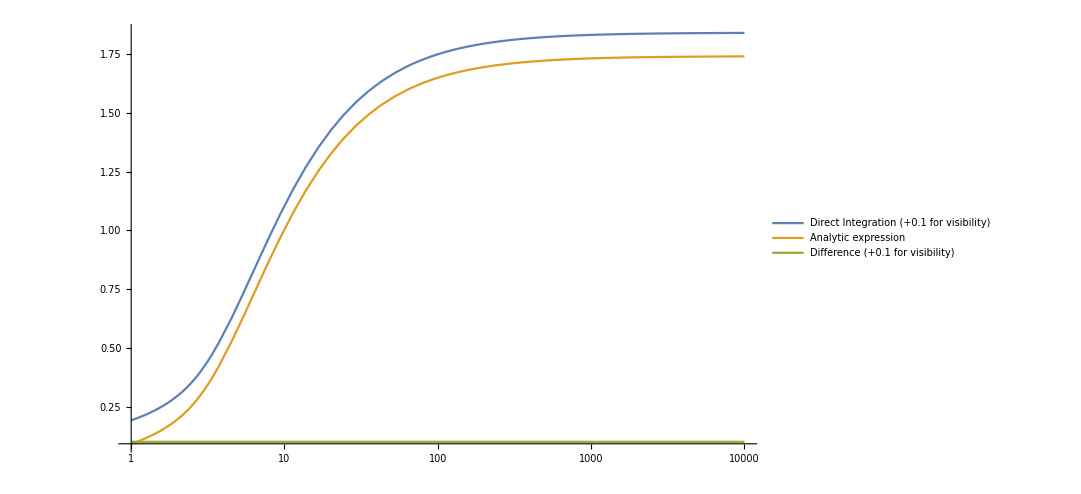

```mathematica
LogLinearPlot[{NIntegrate[2 π vperp bottomFuncMaxwellian[vpar,vperp,vbth[dPhi,Tm],RB,1],{vpar,0,5},{vperp,0,5}]+0.1,LKMwellDensFac[dPhi/T,RB],NIntegrate[2 π vperp bottomFuncMaxwellian[vpar,vperp,vbth[dPhi,Tm],RB,1],{vpar,0,5},{vperp,0,5}]+0.1-LKMwellDensFac[dPhi/T,RB]},{RB,1,10000},PlotRange->All,PlotLegends->{"Direct Integration (+0.1 for visibility)","Analytic expression","Difference (+0.1 for visibility)"},ImageSize->800]
```

```mathematica
NIntegrate[2 π vperp bottomFuncMaxwellian[vpar,vperp,vbth[dPhi,Tm],10,1],{vpar,0,5},{vperp,0,5}]
```

1.00506

```mathematica
2/(√π)NIntegrate[rho^2 Sin[theta] Exp[-rho^2+dPhi/Tm]bottomPieceFuncRho[rho,theta,dPhi/Tm,10],{rho,0,5},{theta,0,π/2}]
```

1.00505